# Oxygen Chemical Potential According to the Shomate Equation

see  the NIST Chemistry Webbook 
https : // webbook.nist.gov/cgi/cbook.cgi?ID = C7782447 & Units = SI & Type = JANAFG & Table = on #JANAFG

## Define functions for enthalpy and entropy:

VERY IMPORTANT: 
1) enthalpy is given in kJ/mol
2) entropy is given in J/mol - K
3) t denotes the reduced temperature T/1000 with T in Kelvin. 
4) These expresssions are valid at atmospheric pressure.  We will add pressure effects later via kT ln(P/P_atm)

```mathematica
enthalpy[t_]:= AA t +1/2 BB t^2+1/3 CC t^3+1/4 DD t^4-EE/t+FF-HH+HoRT  
entropy[t_]:= AA Log[t]+BB t+1/2 CC t^2+1/3 DD t^3-EE/(2 t^2)+GG
```

Choose temperature range of interest:

1) T = 100 - 700 K :

```mathematica
AA=31.32234; BB = -20.23531; CC = 57.86644; DD = -36.50624; EE = -0.007374; FF = -8.903471; GG = 246.7945; HH = 0;  HoRT = 0;
```

2) T = 700 - 2000 K :

```mathematica
AA= 30.03235; BB=8.772972; CC=-3.988133; DD=0.788313; EE=-0.741599; FF=-11.32468; GG=236.1663;  HH=0;HoRT = 0;
```

3) T = 2000 - 6000 K :

```mathematica
AA=20.91111; BB=10.72071; CC=-2.020498; DD=0.146449;EE=9.245722;FF=5.337651;GG=237.6185; HH =0;HoRT = 0;
```

Make plots of enthalpy and entropy

1) Notice that the behavior becomes funny as T approaches 0 Kelvin.  This is a numerical artifact. 
2) The prefactor converts from kJ/mol to eV (enthalpy) or from J/mol-K to eV/K (entropy), so the y axes below both are plotting in units of eV.

```mathematica
Hprefactor=0.01 
Sprefactor=0.00001
```

0.01

0.00001

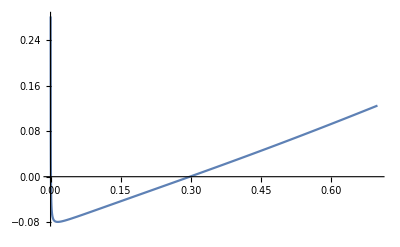

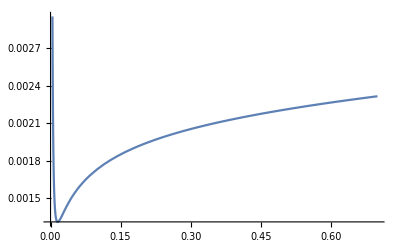

```mathematica
Plot[Hprefactor enthalpy[t],{t,0,0.7}]
Plot[Sprefactor entropy[t],{t,0,0.7}]
```

# Connecting DFT results to real-world temperature and pressure (T,P)

Background

The expression that we use is :
	μ_o(T,P) = 1/2[E_O_2^TOT+(μ̄)_O_2(T,P_atm)+ kT Ln(P/P_atm)]

1) The first term is
	E_O_2^TOT=E_(DFT-PBE)+E_corr+ZPE
is the value of at T = 0 K, P = 1 atm.  Here the three terms are the DFT-PBE energy of O computed in the ground state spin triplet state, the correction to account for the PBE overbinding of the molecule (see Phys. Rev. Lett 80, 890 (1998)), and the zero point energy (all per O_2 molecule). The first number is what I get in VASP using PBE.  All of the units below are in eV per O_2 molecule.

```mathematica
Edftpbe = -9.8593;
Ecorr = 0.9193;
ZPE = 0.1220;
```

2) The second term  (μ̄)_O_2(T,P_atm) represents the shift from the first term (T = 0 K, P = 1 atm) to non-zero temperature, and is  evaluated using the equations above:
		(μ̄)_O_2(T,P_atm)= ΔH - T  ΔS + Δμ       (Gibbs free energy per molecule of O_2)
where the term Δμ is a shift that is present to account for the fact that the ΔH, ΔS Shomate expressions above are relative to RT rather than T = 0.  This is tricky to get, but I will extrapolate the offset between T = 0 K and room temperature as
	at RT (T = 300 K or t = 0.3), the equations above give ΔG = ΔH - T  ΔS = 0 
	at T = 0 K, we have ΔG = ΔH - T  ΔS = ΔH = -29 (0.3) kJ/mol = -0.09017 eV per O_2                 (see below).  
I get this roughly from the slope around t = 0.2 (T = 200 K), which is 29 kJ/mol. 
Therefore the required shift is then Δμ = μ(T = 300 K) - μ(T = 0 K) = 0.09017 eV per O_2.

31.3223-0.007374/t^2-20.2353 t+57.8664 t^2-36.5062 t^3

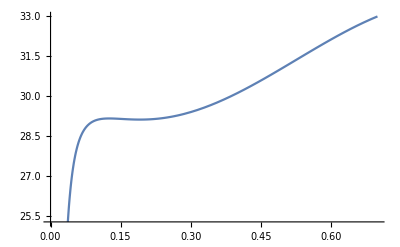

```mathematica
dHdt=D[enthalpy[t],t]
Plot[dHdt,{t,0,0.7}]
```

```mathematica
Δμ=0.09017;
```

3) And then finally the last term allows us to shift to a different pressure from atmospheric.

Put everything together

## Choose temperature range of interest:

1) T = 100 - 700 K :

```mathematica
AA=31.32234; BB = -20.23531; CC = 57.86644; DD = -36.50624; EE = -0.007374; FF = -8.903471; GG = 246.7945; HH = 0;  HoRT = 0;
```

2) T = 700 - 2000 K :

```mathematica
AA= 30.03235; BB=8.772972; CC=-3.988133; DD=0.788313; EE=-0.741599; FF=-11.32468; GG=236.1663;  HH=0;HoRT = 0;
```

3) T = 2000 - 6000 K :

```mathematica
AA=20.91111; BB=10.72071; CC=-2.020498; DD=0.146449;EE=9.245722;FF=5.337651;GG=237.6185; HH =0;HoRT = 0;
```

## Assemble Pieces

```mathematica
Eo2=Edftpbe+Ecorr+ZPE;
Subscript[μ̄, Subscript[O, 2]][T_]:=Hprefactor enthalpy[T/1000]-T Sprefactor entropy[T/1000]+Δμ
kB=8.617333 10^-5;
Subscript[μ, o][T_,P_] := 1/2 (Eo2+Subscript[μ̄, Subscript[O, 2]][T]+kB T Log[P/1])
```

The plot below then shows μ_o at P = 0.1 atm, P = 1 atm, and P = 10 atm as a function of temperature from T = 0 K to T = 700 K. Note that if we want to go to higher ranges of T, we need to choose the right set of parameters in the Shomate equation up at the top.

## Plot Chemical Potentials

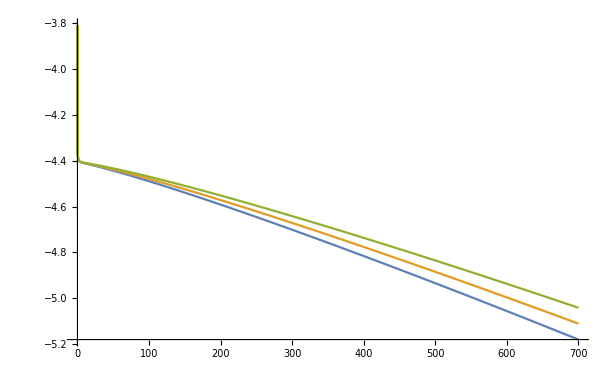

```mathematica
Plot[{Subscript[μ, o][T,0.1],Subscript[μ, o][T,1],Subscript[μ, o][T,10]},{T,0,700}]
```

Here it is, re - evaluated in the higher temperature range:

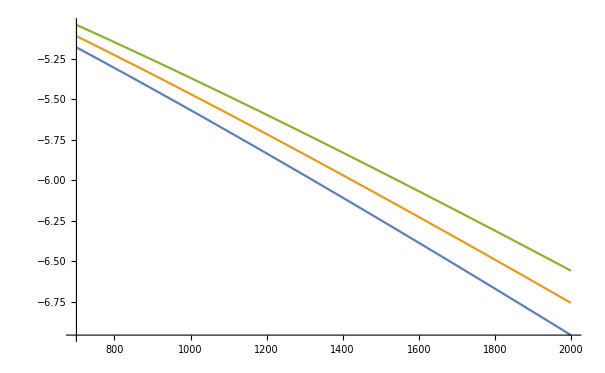

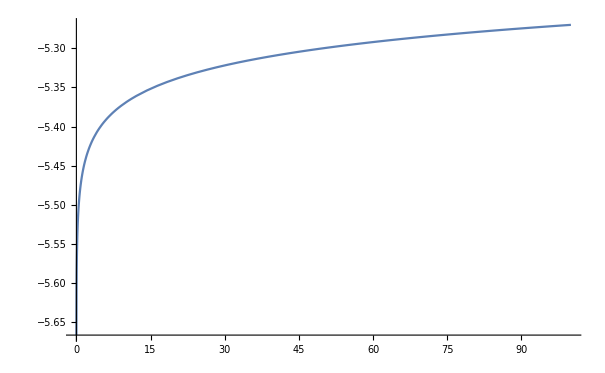

```mathematica
Plot[{Subscript[μ, o][T,0.1],Subscript[μ, o][T,1],Subscript[μ, o][T,10]},{T,700,2000}]
Plot[{Subscript[μ, o][1000,P]},{P,0.01,100},PlotRange->All]
```